Stochastic Simulation

Random number generations

{{1702,952,10001},{65539,0,2147483648},{16807,0,2147483648}}

30

-Graphics3D-

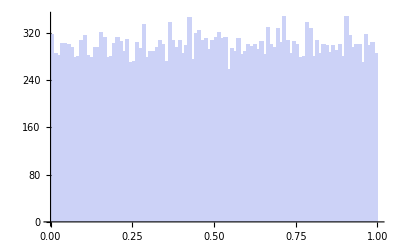

```mathematica
triples={{1702,952,10001},{2^16+3,0,2^31},{7^5,0,2^31}}
{a,b,m}=triples[[3]];
seed=30
randomnumbers=RecurrenceTable[{x[n]==Mod[a*x[n-1]+b,m],x[0]==seed} ,x,{n,0,30000}]/m //N;
Graphics3D[Point[#]& /@Partition[randomnumbers,3],Axes->True]
Histogram[randomnumbers,{.01}]
```

Monte Carlo Integration

```mathematica
fn[n_Integer]:=4*Count[RandomReal[{-1,1},{n,2}],_?(#[[1]]^2+#[[2]]^2≤1&)]/n //N
Table[fn[10^i],{i,6}]
```

{3.2,3.24,3.2,3.1452,3.143,3.13947}

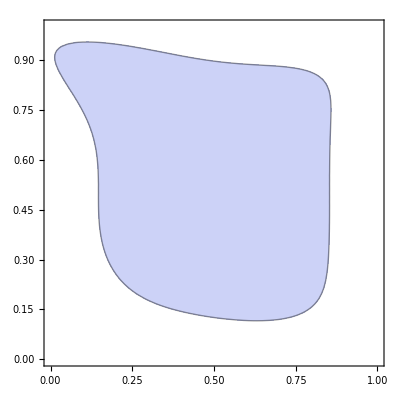

{0.4,0.49,0.528,0.5423,0.54587}

```mathematica
RegionPlot[4(2x-1)^4+8(2y-1)^8<1+2(2y-1)^3(3x-2)^2,{x,0,1},{y,0,1}]
area[n_]:=Count[RandomReal[{0,1},{n,2}],_?(4(2#[[1]]-1)^4+8(2#[[2]]-1)^8≤1+2(2#[[2]]-1)^3(3#[[1]]-2)^2&)]/n //N
Table[area[10^i],{i,5}]
```

Simulation

```mathematica
threecoinflip:=RandomChoice[{"Heads","Tails"},3]
Count[Table[threecoinflip,{i,100000}],{"Heads","Heads","Heads"}]/100000 //N
```

0.12456

```mathematica
montyhall[x_]:=Module[{initial,selection,reveal,switch,noswtich},
initial=RandomSample[{"Goat","Goat","Car"}];
selection=RandomChoice[{1,2,3}];
reveal=RandomChoice[Flatten[Position[initial[[Complement[{1,2,3},{selection}]]],"Goat"]]];
switch=First[Complement[{1,2,3},{selection},{reveal}]];
noswitch=selection;
If[x==True,initial[[switch]],
initial[[noswitch]]]
]
Count[montyhall[#] & /@ConstantArray[False,100000],"Car"]/100000 //N
```

0.33192

Average Random Walks

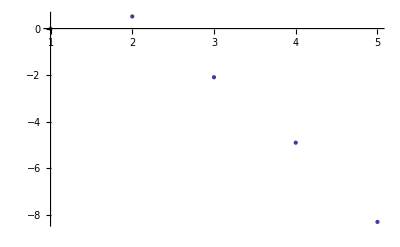

```mathematica
step1d:=RandomChoice[{1,-1}]
step2d:=RandomChoice[{1,-1},2]
step3d:=RandomChoice[{1,-1},3]
aveend1d[n_]:=ParallelTable[Plus @@ Table[step1d,{i,n}],{i,1000}]// Mean //N
ListPlot[Table[aveend1d[10^i],{i,5}]]
```